#### Requirements

```mathematica
Needs["MaTeX`"]
<<MaTeX`
```

# Momentum spectra

## Importing source files

### Defining paths

```mathematica
path="/Users/jordi/Library/CloudStorage/Box-Box/Research/codes/smash";
export path="/Users/jordi/Library/CloudStorage/Box-Box/Research/codes/smash/output";
```

### Data

#### Import function

```mathematica
ImportMomentumSpectrumData[inputFile_]:=
Module[{rawInput,newInput,error},
rawInput=Import[FileNameJoin[{path,inputFile}]];
(* Trim headers *)
newInput=rawInput[[2;;All]];
(* Transpose to obtain a list of columns *)
newInput=Transpose@newInput;
error=newInput[[3]];
(* Re-scale second column *)
newInput=newInput/. {pT_,dNdpT_,error_}:>{pT,1/(2π)1/pT dNdpT,error};
{newInput[[1]],newInput[[2]],newInput[[3]]}
]
```

#### PDG2021+ with full decays

```mathematica
pT p FullDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/full_decays/eBW/N+.dN.dpt.dat"];
pT antip FullDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/full_decays/eBW/anti-N+.dN.dpt.dat"];
pT piplus FullDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/full_decays/eBW/pi+.dN.dpt.dat"];
pT piminus FullDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/full_decays/eBW/pi-.dN.dpt.dat"];
pT Kplus FullDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/full_decays/eBW/K+.dN.dpt.dat"];
pT Kminus FullDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/full_decays/eBW/K-.dN.dpt.dat"];
```

#### PDG2021+ with intermediate decays

```mathematica
pT p IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/intermediate_decays/eBW/N+.dN.dpt.dat"];
pT antip IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/intermediate_decays/eBW/anti-N+.dN.dpt.dat"];
pT piplus IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/intermediate_decays/eBW/pi+.dN.dpt.dat"];
pT piminus IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/intermediate_decays/eBW/pi-.dN.dpt.dat"];
pT Kplus IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/intermediate_decays/eBW/K+.dN.dpt.dat"];
pT Kminus IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["output/PDG2021Plus/intermediate_decays/eBW/K-.dN.dpt.dat"];
```

#### SMASH with full decays

```mathematica
pT p FullDecays SMASH Data=ImportMomentumSpectrumData["output/SMASH/intermediate_decays/eBW/N+.dN.dpt.dat"];
pT antip FullDecays SMASH Data=ImportMomentumSpectrumData["output/SMASH/intermediate_decays/eBW/anti-N+.dN.dpt.dat"];
pT piplus FullDecays SMASH Data=ImportMomentumSpectrumData["output/SMASH/intermediate_decays/eBW/pi+.dN.dpt.dat"];
pT piminus FullDecays SMASH Data=ImportMomentumSpectrumData["output/SMASH/intermediate_decays/eBW/pi-.dN.dpt.dat"];
pT Kplus FullDecays SMASH Data=ImportMomentumSpectrumData["output/SMASH/intermediate_decays/eBW/K+.dN.dpt.dat"];
pT Kminus FullDecays SMASH Data=ImportMomentumSpectrumData["output/SMASH/intermediate_decays/eBW/K-.dN.dpt.dat"];
```

## Plot preparation

```mathematica
AddMomentumSpectra[spectrum1_,spectrum2_,scale_]:=
Module[{totalSpectrum},
totalSpectrum=scale(spectrum1[[2]]+spectrum2[[2]]);
{spectrum1[[1]],totalSpectrum}
]
```

### Intermediate vs. full decays

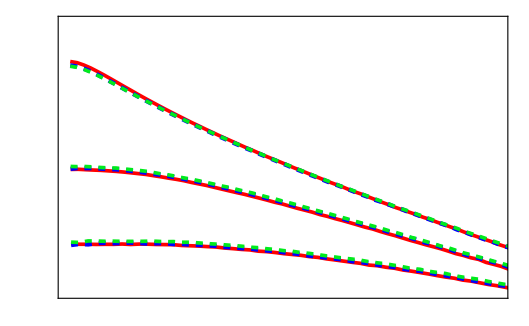
-Graphics--Graphics--Graphics-

```mathematica
PionScale=2;
KaonScale=1;
ProtonScale=0.5;
FullDecaysPDG21PlusScale=1/1787.763;
IntermediateDecaysPDG21PlusScale=1/1669.376;
SMASHScale=1/1613.188;
DirectDecaysPlot=ListLogPlot[{
Transpose@AddMomentumSpectra[pT piplus FullDecays PDG21Plus Data,pT piminus FullDecays PDG21Plus Data,1*FullDecaysPDG21PlusScale*PionScale],
Transpose@AddMomentumSpectra[pT piplus IntermediateDecays PDG21Plus Data,pT piminus IntermediateDecays PDG21Plus Data,1*IntermediateDecaysPDG21PlusScale*PionScale],
Transpose@AddMomentumSpectra[pT piplus FullDecays SMASH Data,pT piminus FullDecays SMASH Data,1*SMASHScale*PionScale],
Transpose@AddMomentumSpectra[pT Kplus FullDecays PDG21Plus Data,pT Kminus FullDecays PDG21Plus Data,1*FullDecaysPDG21PlusScale*KaonScale],
Transpose@AddMomentumSpectra[pT Kplus IntermediateDecays PDG21Plus Data,pT Kminus IntermediateDecays PDG21Plus Data,1*IntermediateDecaysPDG21PlusScale*KaonScale],
Transpose@AddMomentumSpectra[pT Kplus FullDecays SMASH Data,pT Kminus FullDecays SMASH Data,1*SMASHScale*KaonScale],
Transpose@AddMomentumSpectra[pT p FullDecays PDG21Plus Data,pT antip FullDecays PDG21Plus Data,1*FullDecaysPDG21PlusScale*ProtonScale],
Transpose@AddMomentumSpectra[pT p IntermediateDecays PDG21Plus Data,pT antip IntermediateDecays PDG21Plus Data,1*IntermediateDecaysPDG21PlusScale*ProtonScale],
Transpose@AddMomentumSpectra[pT p FullDecays SMASH Data,pT antip FullDecays SMASH Data,1*SMASHScale*ProtonScale]
},
PlotRange->{{0,2},{4*10^-4,2*10^1}},
Frame->True,
FrameStyle->Directive[Thick,Black,16],
FrameTicks->{
{(* primary Y-axis ticks *)
With[{
minorYTicks=Flatten[Table[{j 10^i,"",{0.006,0}},{i,-4,4,1},{j,2,9}],1],
mayorYTicks={
{10^-4,MaTeX["10^{-4}",Magnification->2],{0.015,0}},
{10^-3,MaTeX["10^{-3}",Magnification->2],{0.015,0}},
{10^-2,MaTeX["10^{-2}",Magnification->2],{0.015,0}},
{10^-1,MaTeX["10^{-1}",Magnification->2],{0.015,0}},
{10^0,MaTeX["1",Magnification->2],{0.015,0}},
{10^1,MaTeX["10",Magnification->2],{0.015,0}},
{10^2,MaTeX["10^{2}",Magnification->2],{0.015,0}},
{10^3,MaTeX["10^{3}",Magnification->2],{0.015,0}},
{10^4,MaTeX["10^{4}",Magnification->2],{0.015,0}}
}},
Join[minorYTicks,mayorYTicks]],
(* secondary Y-axis ticks *)
With[{
minorYTicks=Flatten[Table[{j 10^i,"",{0.006,0}},{i,-5,4,1},{j,2,9}],1],
mayorYTicks=Table[{10^i,"",{0.015,0}},{i,-5,4,1}]},
Join[minorYTicks,mayorYTicks]]},
{(* primary X-axis ticks *)
With[{
minorXTicks=Table[i,{i,0,3,0.1}],
mayorXTicks={0,0.5,1,1.5,2,2.5,3}},
Join[{#,"",{0.006,0}} &/@ minorXTicks,
{#,MaTeX[#,Magnification->2],{0.015,0}} &/@ mayorXTicks]],
(* secondary X-axis ticks *)
With[{
minorXTicks=Table[i,{i,0,3,0.1}],
mayorXTicks=Table[i,{i,0,3,0.5}]},
Join[{#,"",{0.006,0}} &/@ minorXTicks,
{#,"",{0.015,0}} &/@ mayorXTicks]]}},
PlotStyle->{
Directive[Thickness[0.005],Red],
Directive[Dashed,Thickness[0.006],Blue],
Directive[Dashing[{Small,Small},0.1,Square],Thickness[0.005],RGBColor[0, 0.92, 0.11]]
},
ImageSize->128*4.135,
PlotLegends->Placed[LineLegend[
MaTeX[{
"1\\rightarrow\\text{all decays},\\, \\text{PDG2021+}",
"1\\rightarrow2\\ \\text{decays},\\, \\text{PDG2021+} ",
"1\\rightarrow2\\ \\text{decays},\\, \\text{SMASH list}"
},FontSize->20],LegendLayout->{"Column",1},LegendMarkers->"",Spacings->0.2],{0.69,0.8}],
Epilog->{
Text[Style[MaTeX[ToString[PionScale]<>"\\times (\\pi^+ + \\pi^-)",Magnification->2]], Scaled[{0.205,0.87}]],
Text[Style[MaTeX["K^+ + K^-",Magnification->2]], Scaled[{0.15,0.52}]],
Text[Style[MaTeX[ToString[ProtonScale]<>"\\times (p+\\overline{p})",Magnification->2]], Scaled[{0.18,0.265}]],
Text[Style[MaTeX["\\text{BW+direct decays}",FontSize->20]], Scaled[{0.79,0.59}]]
},
Joined->True];
LabeledDirectDecaysPlot=Labeled[Show[DirectDecaysPlot,Method->{"ShrinkWrap"->True}],MaTeX[{"\\frac{1}{2\\pi N_\\text{ch}}\\,\\frac{dN}{p_T\\hspace{1mm} dp_T}","p_T\; [\\text{GeV}]"},FontSize->24],{Left,Bottom},Spacings->{0,0},RotateLabel->True]
Export[FileNameJoin[{export path,"Fig_direct_decays_momentum_spectra.pdf"}],LabeledDirectDecaysPlot];
```